# Get started on DMSolitonFinder

Author: Hong-Yi Zhang
Website: https://hongyi18.github.io
Mathematica Version: 13.3.1
Date: Jun 15, 2026

For definitions and equations used in this package, please refer to https://arxiv.org/abs/2406.05031.
For solutions to common problems in finding optimal soliton profiles, please check https://github.com/hongyi18/DMSolitonFinder.

### Package installation

#### Download/update the package

```mathematica
URLDownload["https://raw.githubusercontent.com/hongyi18/DMSolitonFinder/main/DMSolitonFinder.wl", FileNameJoin[{$UserBaseDirectory, "Applications", "DMSolitonFinder.wl"}]]
```

File[C:\Users\hongyi18\AppData\Roaming\Mathematica\Applications\DMSolitonFinder.wl]

#### Load the package

```mathematica
<< "DMSolitonFinder.wl"
```

DMSolitonFinder 1.1 has been loaded.

Please cite [arXiv:2406.05031](https://arxiv.org/abs/2406.05031) if you find this package helpful.

### Basic usage

1. Set the value of the self-interaction (SI) coupling, nonminimal gravitational interaction (NGI) coupling, and polarization number/particle spin.
2. Choose the central amplitude of the soliton profile.
3. Use ShootFields.

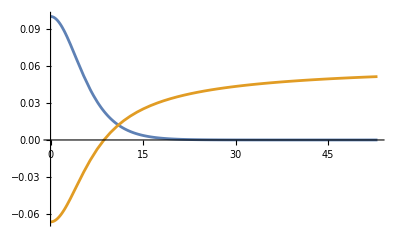

```mathematica
λ = 1; (* SI coupling. *)
ξ = -1; (* NGI coupling. *)
σ = 1; (* Polarization number/particle spin. *)

fi = 1/10; (* Central amplitude of the soliton. *)
ri = 10^-7; (* Location of the inner boundary; default value is 10^-7. *)
{sols, rf} = ShootFields[fi, SI->λ, NGI->ξ, Spin->σ];

Plot[{sols[[1]][r], sols[[2]][r]}, {r, ri, rf}, PlotRange->All] (* Plot f[r] and Ψ[r]. *)
```

Calculate mass, radius, particle number, frequency (chemical potential) and energy.

```mathematica
CalMass[sols[[1]], rf, NGI->ξ]
CalRadius[sols[[1]], rf, NGI->ξ]
CalParticleNumber[sols[[1]], rf]
μ = CalFrequency[sols[[2]], rf]
CalEnergy[sols[[1]], sols[[2]], μ, rf, NGI->ξ]
```

6.89846

11.175

6.89846

0.0616555

-0.128052

### Advanced usage

#### Print the Schroedinger-Poisson equations and the mass density ρ_ξ.

```mathematica
Eqf[f, Ψ, r, SI->λ, NGI->ξ, Spin->σ]
EqPsi[f, Ψ, r, NGI->ξ]
MassDensity[f, r, NGI->ξ]
```

f[r]^3/12+f[r] Ψ[r]+1/2 (-(2 f'[r])/r-f''[r])-f[r] (f[r]^2-2 (f'[r]^2+f[r] ((2 f'[r])/r+f''[r])))

f[r]^2-(2 Ψ'[r])/r-2 (f'[r]^2+f[r] ((2 f'[r])/r+f''[r]))-Ψ''[r]

f[r]^2-2 (f'[r]^2+f[r] ((2 f'[r])/r+f''[r]))

The field equations can be numerically solved using SolveFields.
Example: Given the boundary values of f[r] and Ψ[r] at r=ri, solve the field equations between r=ri and r=rf with the Runge-Kutta method.

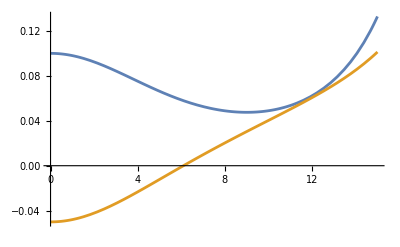

```mathematica
fi = 1/10;
Ψi = -5/100;

ri = 10^-8;
rf = 15;
sols = SolveFields[fi, Ψi, rf, SI->λ, NGI->ξ, Spin->σ, MinRadius->ri, Method->"ExplicitRungeKutta"];

(* Plot the field f[r] and Ψ[r], which are sols[[1]][r] and sols[[2]][r] respectively. *)
Plot[{sols[[1]][r], sols[[2]][r]}, {r, ri, rf}]
```

For more details about the function, check the usage message by running “?FunctionName”.

```mathematica
?SolveFields
```

#### If ShootFields fails to find soliton profiles, try changing the default options.

For fi=9/1000, increasing rf doesn't improve results after 84 calculations, relative amplitude at large radius is 594.547.

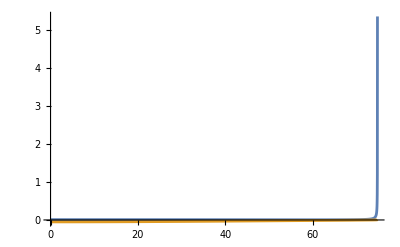

```mathematica
λ = 5000; (* SI coupling. *)
ξ = 0; (* NGI coupling. *)
σ = 0; (* Polarization number/particle spin. *)

fi = 9/1000; (* Central amplitude of the soliton. *)
ri = 10^-7; (* Location of the inner boundary; default value is 10^-7. *)
{sols, rf} = ShootFields[fi, SI->λ, NGI->ξ, Spin->σ, Method->"ExplicitRungeKutta"];

Plot[{sols[[1]][r], sols[[2]][r]}, {r, ri, rf}, PlotRange->All] (* Plot f[r] and Ψ[r]. *)
```

Adjust the value of the option “FirstMinimumLocationRatio” might help:

For fi=9/1000, requested precision is reached after 100 calculations, relative amplitude at large radius is 0.000584759.

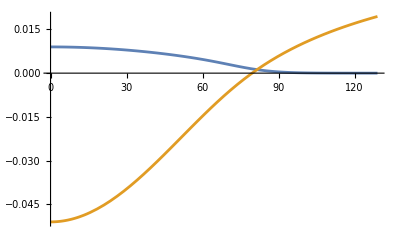

```mathematica
λ = 5000; (* SI coupling. *)
ξ = 0; (* NGI coupling. *)
σ = 0; (* Polarization number/particle spin. *)

fi = 9/1000; (* Central amplitude of the soliton. *)
ri = 10^-7; (* Location of the inner boundary; default value is 10^-7. *)
{sols, rf} = ShootFields[fi, SI->λ, NGI->ξ, Spin->σ, Method->"ExplicitRungeKutta", FirstMinimumLocationRatio->93/100];

Plot[{sols[[1]][r], sols[[2]][r]}, {r, ri, rf}, PlotRange->All] (* Plot f[r] and Ψ[r]. *)
```

For more solutions to common problems in finding optimal soliton profiles, please check https://github.com/hongyi18/DMSolitonFinder.